```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
InitializationValue[$Initialization] = Hold[$HistoryLength = 2];
```

```mathematica
Clear[MyGraph];
Options[MyGraph]={"undirected" ->True,"label" ->False};
MyGraph[edges__,root_,source_,OptionsPattern[]]:={Module[{locEdges={},i,locWeights={},locRoot=root,locSource=source,p},
Clear[β];

For[i=1, i<=(Dimensions@edges)[[1]],i++,
If[OptionValue["undirected"] && edges[[i,2]] =!=locSource && edges[[i,2]] =!=edges[[i,1]] ,
AppendTo[locEdges,edges[[i,2]]->edges[[i,1]]];
AppendTo[locWeights,β[edges[[i,2]],edges[[i,1]]] ]
];

If[edges[[i,1]]==locSource,Continue[]];

AppendTo[locEdges,edges[[i,1]]->edges[[i,2]]];
AppendTo[locWeights,β[edges[[i,1]],edges[[i,2]]] ]
];

locEdges=Sort[locEdges,(#1[[1]]<=#2[[1]] &&#1[[2]]<=#2[[1]])||(#1[[1]]<#2[[2]] &&#1[[2]]<=#2[[2]]) &];

p[β[a_,b_],β[c_,d_]]:=1/;(a<=c&&b<=c);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<=a&&d<=a);
p[β[a_,b_],β[c_,d_]]:=1/;(a<d&&b<=d);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<b&&d<=b);
locWeights=Sort[locWeights,p];

(*Print[locEdges];
Print[locWeights]*);

If[ OptionValue["label"],
(*True*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, EdgeLabels->"EdgeWeight", VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]]
],
root(*Root*),source(*Source*)}
```

```mathematica
Clear[DrawOnGraph];
Options[DrawOnGraph]={"drawOthers"-> True};
DrawOnGraph[graph_,path__,OptionsPattern[]]:=Module[{locEdges,locPathStyle={},locRoot,locSource,i},
locEdges = EdgeList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

For[i=1, i<=Length[path],i++,
AppendTo[locPathStyle,{path[[i,1]]->path[[i,2]]->path[[i,3]]}];
(*Print[locPathStyle]*)
];
If[OptionValue["drawOthers"],
(*True*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,Blue}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,White}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]
]
]
```

```mathematica
path1={{2,1,Red},{1,3,Green}};
DrawOnGraph[g,path1]
```

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{2->1→RGBColor[1, 0, 0],1->3→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

```mathematica
Clear[DrawFromExpression];
Options[DrawFromExpression]={"graph"->g,"drawOthers"->False};

DrawFromExpression[exp_,OptionsPattern[]]:=Module[{terms,graphs={},i},
terms=exp//.R[a_,b_,c_]^n_->R[a,b,c]//Expand;
terms=List @@ (terms+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->OptionValue["drawOthers"]]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];
]
```

```mathematica
Clear[AugmentedGraph];
AugmentedGraph[graph_]:=Module[{locVertices,locEdges,locPathStyle={},locRoot,locSource,newSource,oldSourceNeighbors,graphPlus,i},

locVertices = VertexList@graph;
locEdges = EdgeList@graph/.DirectedEdge->List;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

newSource=locVertices[[-1]]+1;

(*Add the edge from the oldSource to the newSource*)
AppendTo[locEdges,{locSource,newSource}];

(*Add all the edges from the oldSource to its neighbors*)
oldSourceNeighbors=Select[locEdges, #[[2]]==locSource &];

For[i=1,i<=Length[oldSourceNeighbors],i++,
AppendTo[locEdges,{locSource,oldSourceNeighbors[[i,1]]}]
];

graphPlus =MyGraph[locEdges,locRoot,newSource,"undirected"->False][[1]];

Return[{graphPlus,locSource,newSource}]
]
```

```mathematica
Clear[monoFlatten];
(*monoFlatten[a_?NumericQ]:={};*)
monoFlatten[a_]:={a};
monoFlatten[{a__}]:={{a}};
monoFlatten[{a__,b__}]:={a,b};
```

```mathematica
Clear[ExtractPaths];
ExtractPaths[exp_]:=Module[{terms,paths={},i},

terms=exp//Expand;
terms=List @@Collect[terms,R[__,Red]];
terms=Outer[List,terms];

For[i=1,i<=Length[terms],i++,
If[MatchQ[terms[[i,1]],R[__,Red]*A_],
AppendTo[paths,terms[[i]]]
]
];
terms=paths//.R[__,Blue]->1//FullSimplify;

Return[terms]
]
```

```mathematica
Clear[V];
V[1.]:=1.;
V[1]:=1;
V[0]:=0;
V'[a_]:=1
```

```mathematica
Clear[VertexAssignment];
Options[VertexAssignment]={"system"->"LERW","print"->False,"excludedVertices"->{},"sourceBC"->1};

VertexAssignment[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,locSource,action,x,y},
Clear[i];
locVertices=VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

(*LERW*)
If[OptionValue["system"]=="LERW",
If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
action = Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Sum[locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]]χ[x,Subscript[i, x]],{y,Length[locVertices]}] ) ]],{x,Length[locVertices]}];
action*=V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[i, s]])];(*This is the BC*)
Return[action]];

(*DLA*)
If[OptionValue["system"]=="DLA",If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
Return[
Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Product[1+locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]],{y,Length[locVertices]}] χ[x,Subscript[i, x]]+ Sum[locWeights[[x,y]]/totWeights[[x]] ϕs[y,Subscript[j, x]]ϕ[x,Subscript[j, x]],{y,Length[locVertices]}])] ],{x,Length[locVertices]}]
]]
]
```

```mathematica
ClearAll[Σδrule];
Σδrule={δ[a_,b_]^n_/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,b]^(n-2) δ[a,a],
δ[b_,a_]δ[c_,b_]/;(!NumericQ[b] && !MatchQ[b,Subscript[1, __]]):>δ[c,a],
δ[a_,b_]δ[c_,b_]/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,c],
δ[a_,a_]/;(MatchQ[a,Subscript[i, __]])/;(a=!=Subscript[i, s]):>n,
δ[a_,a_]/;(MatchQ[a,Subscript[j, __]])/;(a=!=Subscript[j, s]):>n,
δ[a_,a_]/;(MatchQ[a,Subscript[k, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[l, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[ll, _]]):>1};
```

```mathematica
ClearAll[δruleExternal];
δruleExternal={δ[a_,a_]/;(NumericQ[a] || a==Subscript[i, s] || MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[1, __]]|| MatchQ[a,Subscript[jjj, __]] ||MatchQ[a,Subscript[k, _]]):>1,
δ[a_,b_]/;(NumericQ[a] ||MatchQ[a,Subscript[k, _]]|| MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[1, _]]|| MatchQ[a,Subscript[jjj, __]] )/;(a=!=b):>0,
δ[a_,b_]/;(NumericQ[b] ||MatchQ[b,Subscript[k, _]]|| MatchQ[b,Subscript[j, __]]|| MatchQ[a,Subscript[1, _]]|| MatchQ[a,Subscript[jjj, __]] )/;(a=!=b):>0 };
```

```mathematica
Clear[Op];
Op[1]:=1;
Op[0]:=0;
Op'[_]:=1
```

```mathematica
Clear[FieldsNamesGenerator];
FieldsNamesGenerator[fields_]:=
FieldsNamesGenerator[fields]=Block[{locFields={},starFields={},deltaFields={},deltaStarFields={},l},

locFields=fields;

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

Return[{locFields,starFields,deltaFields,deltaStarFields}]
]
```

```mathematica
Clear[WickContractionBlock];
Options[WickContractionBlock]={"print"->False,"fields"->{χ}, "endTime"->1,"#vertices"->10};

WickContractionBlock[A_ +B_,OptionsPattern[]]:=WickContractionBlock[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]]+
WickContractionBlock[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]];

WickContractionBlock[Op[A_ +B_]*C_,OptionsPattern[]]:=WickContractionBlock[Op[A]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]]+
WickContractionBlock[Op[B]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]];

WickContractionBlock[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContractionBlock[V[A_] *B_, OptionsPattern[]]:=Block[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,κ,jj,l,timeIndex},

z=V[A]B;

(*
If[OptionValue["print"],
Print["###################  Partition Function  ##################"];
];*)

(* Updated version with FieldsNamesGenarator
locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]]
];(*End of loop to define the fields*)
*)

locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];


(*Start a loop over time*)
For[timeIndex=0,timeIndex<=(OptionValue["endTime"]-1),timeIndex++,

z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[jj=1,jj<=OptionValue["#vertices"],jj++,

(*First contribution*)
zTemp1=z//.locFields[[l]][jj,a_]->0//.starFields[[l]][jj,a_]->0;
If[zTemp1-z=!=0,
contributions=zTemp1;
(*Print["First contribution: ",zTemp1];*)
];

(*Second contribution*)
zTemp1=z/. locFields[[l]][jj,a_]->locFields[[l]][jj,a]+κ *deltaFields[[l]][jj,a];
If[zTemp1-z=!=0,
zTemp1=D[zTemp1,κ]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][jj,a_]->starFields[[l]][jj,a]+κ *deltaStarFields[[l]][jj,a];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,κ]/.κ->0;
];

zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

zTemp1=zTemp2/.deltaFields[[l]][jj,a_]->0/.deltaStarFields[[l]][jj,b_]->0;


If[contributions-zTemp1=!=0,
contributions+=zTemp1;
(*Print["Second contribution: ",zTemp1];*)
];


(*THIRD contribution*)
zTemp1=z/. locFields[[l]][jj,a_]->locFields[[l]][jj,a]+κ *deltaFields[[l]][jj,a];
If[zTemp1-z=!=0,
zTemp1=1/2 D[zTemp1,{κ,2}]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][jj,a_]->starFields[[l]][jj,a]+κ *deltaStarFields[[l]][jj,a];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,{κ,2}]/.κ->0;
];

zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];
zTemp2=zTemp1//.deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_]*deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b]*δ[a,b];

zTemp1=zTemp2/.deltaFields[[l]][jj,a_]->0/.deltaStarFields[[l]][jj,b_]->0;

If[contributions-zTemp1=!=0,
contributions+=zTemp1;
(*Print["Third contribution: ",zTemp1];*)
];

z=contributions;


(*Print["Overall contributions: ",contributions];
Print["################################"];*)

contributions=0;

];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

];(*End of loop over fields*)

(*For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0
];*)

z=z//.Σδrule;

];(*End of loop over time*)

Return[z]
];
```

```mathematica
Clear[ExpectationValueBlock];
Options[ExpectationValueBlock]={"operator"->1,"print"->False, "fields"->{χ},"endTime"->1,"draw"->False,"graph"->g, "Rrule"->{R[__]->1},"externalδ"->True,"nχ"->-1,"nα"->0};

ExpectationValueBlock[Z_,OptionsPattern[]]:=Block[{Nvertices,z,terms,graphs={},i},

Nvertices=Length[VertexList@OptionValue["graph"]];

If[OptionValue["operator"]===1,
(*True*)z=WickContractionBlock[Z,
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices
],
(*False*)z=WickContractionBlock[Z*Op[OptionValue["operator"]],
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices
]/WickContractionBlock[Z, "fields"->OptionValue["fields"],"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices]
];

If[OptionValue["externalδ"],
z=z//.δruleExternal
];

z=z/.n->OptionValue["nχ"];
z=z/.m->0;

If[OptionValue["draw"],
(*True*)
z=z//.R[a_,b_,c_]^n_->R[a,b,c];
terms=List @@ (z+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];
z=z/.R[___]->1;
(*
For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->False]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
]*);,

(*False*)z=z/.OptionValue["Rrule"]];

Return[z]]
```

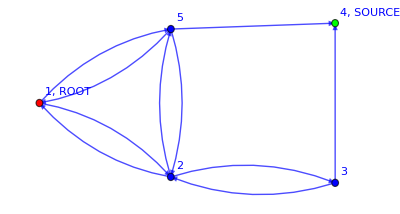

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

```mathematica
Clear[LERWtransitionProb];
Options[LERWtransitionProb]={"draw"->False,"print"->False};

LERWtransitionProb[graph_,path__,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,denominator,prob=1, Z,numerator},
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Return[NULL]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Return[NULL]];

Module[{locBC={{},{}},ϕ,i=1,j},
locBC={{ϕ[locSource]==1},{locSource}};

For[i=1,i<=Length[path],i++,

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z*χs[path[[i,1]],1]];

If[OptionValue["print"],
Print["#####  Previous Partition Function  #####"];
Print[Z]
];

denominator=Z//FullSimplify;


(*Then we need to solve it again with updated BC at the current step*)

AppendTo[locBC[[1]],ϕ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];
(*Print[locBC]*);


Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]],"sourceBC"->denominator^-1];
Z=ExpectationValue[Z*χs[path[[i,2]],1] ];

If[OptionValue["print"],
Print["#####  Current Partition Function  #####"];
Print[Z]
];

numerator=locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Z//FullSimplify;

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[numerator/.β[_,_]->1//FullSimplify];

prob*=numerator//FullSimplify;
]
];
If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

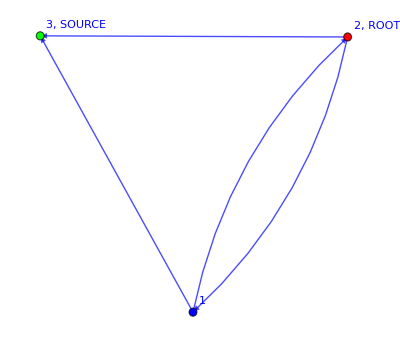
LaplacianRW[-Graphics-,{{2,1},{1,3}}]

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];

path1={{2,1},{1,3}};
LaplacianRW[g,{{2,1},{1,3}}](*/.β[_,_]->1*)
```

```mathematica
Clear[Znorm];
Options[Znorm]={"graph"->g,"fieldsToExclude"->{ϕs,ψs},"theory"->"LERW","βrule"->{β[__]->1.}};

Znorm[expression_,OptionsPattern[]]:=Block[{locZnorm,excludedVertices,token,index},

excludedVertices=(expression * 2)/.R[__]->1/.γ->1//Expand;
excludedVertices=List @@excludedVertices;
excludedVertices=excludedVertices[[2;;]]; (*Gets rid of the numerical coefficient*)

For[index=1,index<=Length[OptionValue["fieldsToExclude"]],index++,
excludedVertices=excludedVertices/.OptionValue["fieldsToExclude"][[index]][a_,__]->a;
];
(*excludedVertices=excludedVertices/.ψs[a_,__]->a;
excludedVertices=excludedVertices/.ψs[a_,__]ψs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]ξs[a_,__]->a;*)

locZnorm=VertexAssignment[OptionValue["graph"],"system"->"LERW","excludedVertices"->excludedVertices]/.OptionValue["βrule"];

ExpectationValueBlock[locZnorm * token,"graph"->OptionValue["graph"],"fields"->FieldsNamesGenerator[{ϕ,χ}]]/.token->1
]
```

```mathematica
Clear[LRWaction];
Options[LRWaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWaction[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
g=myFavoriteGraph;
endTime=1;
Z=LRWaction["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
Clear[bLRWaction];
Options[bLRWaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

bLRWaction[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]ξs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}])(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]ξs[y,Subscript[t, T],Subscript[j, x]]ξ[x,Subscript[t, T],Subscript[j, x]],{y,Length[locVertices]}])
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
],{x,Length[locVertices]}]
V[( ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+(1+χ[locSource,Subscript[t, T],1])*(1+ξ[locSource,Subscript[t, T],1]))];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

```mathematica
Clear[bLRWnorm];
Options[bLRWnorm]={"graph"->g,"endTime"->endTime,"fieldsToExclude"->{ϕs,ψs},"theory"->"LERW","βrule"->{β[__]->1.},"fields"->FieldsNamesGenerator[{ϕ,χ,ξ,ψ}]};

bLRWnorm[expression_,OptionsPattern[]]:=Block[{locZnorm,excludedVertices,token,index},

excludedVertices=(expression * 2)/.R[__]->1/.γ->1//Expand;
excludedVertices=List @@excludedVertices;
excludedVertices=excludedVertices[[2;;]]; (*Gets rid of the numerical coefficient*)

For[index=1,index<=Length[OptionValue["fieldsToExclude"]],index++,
excludedVertices=excludedVertices/.OptionValue["fieldsToExclude"][[index]][a_,__]->a;
];
(*excludedVertices=excludedVertices/.ψs[a_,__]->a;
excludedVertices=excludedVertices/.ψs[a_,__]ψs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]ξs[a_,__]->a;*)

locZnorm=bLRWaction["graph"->g,"endTime"->OptionValue["endTime"],"excludedVertices"->excludedVertices]/.OptionValue["βrule"];(*VertexAssignment[OptionValue["graph"],"system"->"LERW","excludedVertices"->excludedVertices]/.OptionValue["βrule"];*)

ExpectationValueBlock[locZnorm *token,"endTime"->OptionValue["endTime"],"fields"->OptionValue["fields"],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->OptionValue["graph"]]/.token->1
(*ExpectationValueBlock[locZnorm * token,"graph"->OptionValue["graph"],"fields"->FieldsNamesGenerator[{ϕ,χ,ξ}]]/.token->1*)
]
```

```mathematica
Clear[ConvergencebLRW];
Options[ConvergencebLRW]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,ξ,χ}],"steps"->10,"precision"->10^-9,"gammaValue"->0.1};

ConvergencebLRW[operator_,OptionsPattern[]]:=Module[{Z,locOperator,locPrecision,locγ,exp,i,temp,token},

i=1;

Z=bLRWaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1;

locOperator= operator /bLRWnorm[operator,"graph"->OptionValue[ "graph"],"endTime"->1,"βrule"->{β[__]->1},"fields"->OptionValue["fields"]];

locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=ExpectationValueBlock[Z locOperator,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

(*Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)]<>" ############"];*)

For[i=2,i<=OptionValue["steps"] (*&& (Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)>=locPrecision*),i++,

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(bLRWnorm[a,"graph"->OptionValue[ "graph"],"endTime"->1,"βrule"->{β[__]->1},"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

];


Print["########## i=",i-1,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

Return[exp];
]
```

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];
g=myFavoriteGraph;
endTime=1;
Z=bLRWaction["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
Clear[LaplaceEqSolver];
Options[LaplaceEqSolver]={"BC"->{{},{}} , "selectSolution"->0};

LaplaceEqSolver[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,locRoot,locSource,locBC,equations,variables={},x,solution},
Clear[Φ];

locVertices = VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

locBC=OptionValue["BC"];

If[locBC=!={{},{}},

AppendTo[locBC[[1]],Φ[locSource]== 1];
AppendTo[locBC[[1]],Φ[locRoot]==0];

AppendTo[locBC[[2]],locSource];
AppendTo[locBC[[2]],locRoot];
];

equations =locBC[[1]] ;

For[x=1,x<=Length[locVertices],x++,
AppendTo[variables,Φ[x]];
If[MemberQ[locBC[[2]],x],Continue[]];
AppendTo[equations, Φ[x]==FullSimplify[Sum[locWeights[[x,y]]/totWeights[[x]] Φ[y],{y,Length[locVertices]}]]]];
(*Print[equations];
Print[variables];*)
solution=Flatten@Solve[equations,variables]/. Rule->List;

If[OptionValue["selectSolution"]!=0,(*True*)
solution=Select[solution,#[[1]]==Φ[OptionValue["selectSolution"]] &][[1,2]]
];

Return[solution]
]
```

```mathematica
Clear[bLaplacianRW];
Options[bLaplacianRW]={"draw"->False,"print"->False};
bLaplacianRW[graph_,path__,b_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,locVertices,denominator,prob=1},
locWeights=WeightedAdjacencyMatrix[graph]/.β[__]->1//Normal;
locVertices=VertexList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Abort[]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Abort[]];

Module[{locBC={{},{}},ϕ,i,ϕsol},

AppendTo[locBC[[1]],Φ[locSource]==1];
AppendTo[locBC[[2]],locSource];

For[i=1,i<=Length[path],i++,
AppendTo[locBC[[1]],Φ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];

(*Print[locBC];*)

ϕsol=LaplaceEqSolver[graph,"BC"->locBC]/.β[__]->1;
(*Print[ϕsol];*)

(*Print[" ##### OK SO FAR ##### "];*)

denominator=Sum[locWeights[[path[[i,1]],y]]*(Select[ϕsol,#[[1]]==Φ[y] &][[1,2]])^b,{y,Length[locVertices]}];
(*Print[denominator]*);

If[OptionValue["print"],
Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];

Print[(locWeights[[path[[i,1]],path[[i,2]]]]*(Select[ϕsol,#[[1]]==Φ[path[[i,2]]] &][[1,2]])^b)/denominator/.β[_,_]->1//FullSimplify];
];

prob*=(locWeights[[path[[i,1]],path[[i,2]]]]*(Select[ϕsol,#[[1]]==Φ[path[[i,2]]] &][[1,2]])^b)/denominator/.β[__]->1//FullSimplify;
Clear[ϕsol];
];(*END OF FOR*)
];(*END OF MODULE*)

If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

```mathematica
Clear[PathFinder];

PathFinder[graph_]:=Module[{pathList={{}}},
Step[subgraph_]:=Module[{locEdges,locVertices,locWeights,locRoot,locSource,locMoves,newEdges, newRoot,smallerGraph,i},
locEdges = EdgeList@subgraph/.DirectedEdge->List;
locVertices=VertexList@subgraph;
If[Length[locVertices]==1,Return[NULL]];
locWeights=WeightedAdjacencyMatrix[subgraph]//Normal;
locRoot = 
 Select[(List@@@PropertyValue[subgraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[subgraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];
locMoves=Select[locEdges,#[[1]]==locRoot &][[All]];

(*Print["###  LocMoves  ####"];
Print[locMoves];*);

For[i=1, i<=Length[locMoves],i++,

If[i ==Length[locMoves],
(*True*)If[locMoves[[i,2]]==locSource,
 (*Ture*)pathList=Append[pathList[[2;;]],Append[pathList[[1]],locMoves[[i]]]]; Continue[],
 (*False*)pathList=Prepend[pathList[[2;;]],Append[pathList[[1]],locMoves[[i]]]]
],
(*False*)
If[locMoves[[i,2]]==locSource,
 (*True*)pathList=Append[pathList,Append[pathList[[1]],locMoves[[i]]]];Continue[],
 (*False*)pathList=Prepend[pathList,Append[pathList[[1]],locMoves[[i]]]]
]];

(*Print["###  pathList  ####"];
Print[pathList];*);

newEdges=Select[locEdges,#[[1]]=!=locRoot && #[[2]]=!=locRoot &][[All]];
newRoot = locMoves[[i,2]];
If[Length[newEdges] <= 0,Continue[]];
smallerGraph=MyGraph[newEdges,newRoot,locSource,"undirected"->False][[1]];

(*Print[smallerGraph];*);

Step[smallerGraph]
]
];

Step[graph];
Return[pathList]
]
```

```mathematica
Clear[AllbLaplacianRWs]

Options[AllbLaplacianRWs]={"draw"->False,"print"->False};

AllbLaplacianRWs[graph_,b_,OptionsPattern[]]:=Module[{possibleLRW,i,probabilityLRW={}},
possibleLRW=PathFinder[graph];
For[i=1, i<= Length[possibleLRW],i++,
AppendTo[probabilityLRW,bLaplacianRW[graph,possibleLRW[[i]],b,"draw"->OptionValue["draw"]]];

If[OptionValue["print"],Print[i,") Laplacian RW ",possibleLRW[[i]]," with probability " ,probabilityLRW[[i]]]
]
];

possibleLRW=
Replace[possibleLRW,{a_?NumberQ,c_?NumberQ}:>R[a,c,RGBColor[1, 0, 0]],3];

Return[{possibleLRW,probabilityLRW}]
]
```

```mathematica
Clear[b];
```

```mathematica
Clear[AllbLaplacianRWs]

Options[AllbLaplacianRWs]={"draw"->False,"print"->False};

AllbLaplacianRWs[graph_,b_,OptionsPattern[]]:=Module[{possibleLRW,i,probabilityLRW={}},
possibleLRW=PathFinder[graph];
For[i=1, i<= Length[possibleLRW],i++,
AppendTo[probabilityLRW,bLaplacianRW[graph,possibleLRW[[i]],b,"draw"->OptionValue["draw"]]];

If[OptionValue["print"],Print[i,") Laplacian RW ",possibleLRW[[i]]," with probability " ,probabilityLRW[[i]]]
]
];
Return[{possibleLRW,probabilityLRW}]
]
```